```mathematica
(*Aproximación usando la serie de Taylor*)
```

```mathematica
ClearAll[f]
```

```mathematica
Nd=3; (*orden*)
f[x_]:=Cos[x];(*Función*)
```

```mathematica
(*Código artesanal*)
Derivadas={f[x0]};
Do[
temp=D[f[x0],{x0,n}];
If[temp=== 0,Break[],AppendTo[Derivadas,(temp*(x-x0)^n)/Factorial[n]]]
,{n,1,Nd}(*Infinity*)
](*end Do*);
```

```mathematica
resul=Total[Derivadas]
f1[x_]:=resul/.x0-> 0
```

Cos[x0]-1/2 (x-x0)^2 Cos[x0]-(x-x0) Sin[x0]+1/6 (x-x0)^3 Sin[x0]

```mathematica
(*Usando función de Mathematica*)
```

```mathematica
matSer = Series[f[x],{x,x0,Nd}]//Normal
f2[x_]:=matSer/.x0-> 0
```

Cos[x0]-1/2 (x-x0)^2 Cos[x0]-(x-x0) Sin[x0]+1/6 (x-x0)^3 Sin[x0]

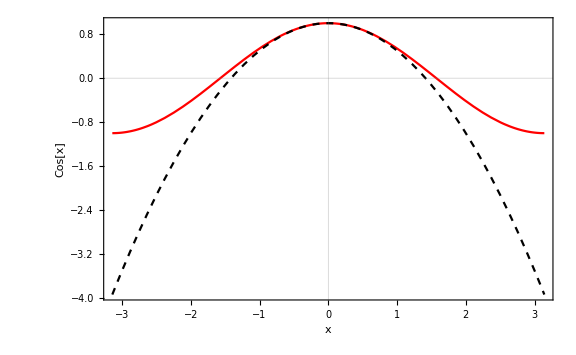

```mathematica
(*Comparando*)
Plot[{Cos[x], f2[x]},{x,-π,π}, PlotStyle->{Red,{Dashed,Black}},PlotTheme->"Scientific",ImageSize->Large, FrameLabel->{"x","Cos[x]"}]
```